# 4QFT on SiDelft

### Modules

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, plotglobalphase:False]. Calculate distance of 2 matrices by max_λ |(U-V)|, 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,plotglobalphase_:False]:=Module[{globalphase,mindist,F,ϕ},
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"}]];
{mindist,ϕ/.globalphase}
]
HSDistance::usage="HSDistance[ansatz,θvars,unitary,nqubits]";
HSDistance[ansatz_,θvars_,unitary_,nqubits_]:=Module[{ρ,ψ,f},
ρ=CreateDensityQureg[2*nqubits];
ψ=CreateQureg[2*nqubits];
ApplyCircuit[InitZeroState@ψ,bellpairs[nqubits]];
ApplyCircuit[InitZeroState@ρ,bellpairs[nqubits]];
ApplyCircuit[ρ,{Subscript[U, Sequence@@Range[0,nqubits-1]][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,ansatz/.θvars];
f=CalcFidelity[ρ,ψ];
DestroyQureg/@{ρ,ψ};
1-f
]
bellpairs::usage="create n-bell pairs";
bellpairs[n_,reverse_:False]:=With[{bp=Flatten[{Subscript[H, #1],Subscript[C, #1][Subscript[X, #2]]}&@@@Transpose@{Range[0,n-1],Range[n,2n-1]}]},If[reverse,Reverse@bp,bp]]
checkedConfψ[nqubit_,unitary_,ntrainstates_]:=Module[{conf,a},
While[True,
conf=DefaultConfig[nqubit,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStatesψ[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

checkedConfρ[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

varMeanInitStatesψ::usage="varMeanInitStates[conf]. Calculate mean and variance of initial random states applied to the unitary.";
varMeanInitStatesψ[conf_]:=Module[{weights,ψwork,ψ,vm,g},
ψwork=CreateQureg[conf["nqubit"]];
ψ=CreateQureg[conf["nqubit"]];
vm=Association[
Table[
CloneQureg[ψ,conf["ψinit"][k]];
ApplyCircuit[ψ,conf["undocirc"][k]];
g=Calc2QubitCorr[conf["nqubit"],ψ,ψwork];
weights=PropertyValue[g,EdgeWeight];
k->{Mean[weights],Variance[weights]}
,{k,Keys@conf["ψinit"]}]];
DestroyQureg[ψwork];
DestroyQureg[ψ];
vm
]
```

### Definition of ansatze and sanity check

```mathematica
ansatz={Subscript[Rx, 0][Subscript[θ, 120]],Subscript[Ry, 3][Subscript[θ, 56]],Subscript[Ry, 0][Subscript[θ, 123]],Subscript[C, 2][Subscript[Ph, 3][Subscript[θ, 59]]],Subscript[Rx, 0][Subscript[θ, 124]],Subscript[SWAP, 1,2],Subscript[Ry, 1][Subscript[θ, 42]],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 50]]],Subscript[Ry, 0][Subscript[θ, 7]],Subscript[C, 1][Subscript[Ph, 2][Subscript[θ, 33]]],Subscript[Rx, 0][Subscript[θ, 17]],Subscript[SWAP, 2,3],Subscript[Rx, 1][Subscript[θ, 9]],Subscript[C, 2][Subscript[Ph, 3][Subscript[θ, 11]]],Subscript[SWAP, 2,3],Subscript[Rx, 3][Subscript[θ, 15]],Subscript[Ry, 2][Subscript[θ, 68]],Subscript[Ry, 3][Subscript[θ, 16]],Subscript[Rx, 2][Subscript[θ, 69]],Subscript[SWAP, 1,2],Subscript[SWAP, 2,3],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 97]]],Subscript[SWAP, 1,2],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 103]]],Subscript[Ry, 0][Subscript[θ, 104]],Subscript[SWAP, 1,2],Subscript[SWAP, 2,3]};
θvars=<|Subscript[θ, 7]->3.1415553081326135,Subscript[θ, 9]->-3.1415902761443144,Subscript[θ, 11]->-5.497781449174974,Subscript[θ, 15]->3.141592396414565,Subscript[θ, 16]->3.141589972815106,Subscript[θ, 17]->-3.141586998968119,Subscript[θ, 33]->-1.5707929977286346,Subscript[θ, 42]->1.570798121323009,Subscript[θ, 50]->-0.7853987794252625,Subscript[θ, 56]->-1.5708008555616957,Subscript[θ, 59]->1.5707925829678986,Subscript[θ, 68]->1.570804921837841,Subscript[θ, 69]->-1.570796911567822,Subscript[θ, 97]->1.5707970860430527,Subscript[θ, 103]->0.3927006396217121,Subscript[θ, 104]->1.5707772216030695,Subscript[θ, 120]->-1.5707621567171606,Subscript[θ, 123]->0.7853977194886816,Subscript[θ, 124]->1.5707583339002782|>;
```

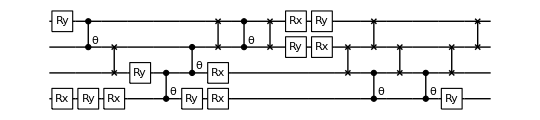

```mathematica
DrawCircuit[ansatz,4]
```

Distances given pristine qubits

```mathematica
unitary=CalcCircuitMatrix[DeleteCases[GetKnownCircuit["QFT",4],Subscript[SWAP, __]]];
```

```mathematica
MatrixDist[unitary,CalcCircuitMatrix[ansatz/.θvars]]
```

{0.0000172466,1.1781}

```mathematica
HSDistance[ansatz,θvars,unitary,4]
```

1.16544×10^-10

Use native gates, refine the search and check the new distance for sanity check

```mathematica
CustomGatesDefinitions
```

{SWAP_(p_,q_):>Sequence@@{Rx_p[π/2],C_p[Z_q],Rx_p[π/2],Rx_q[π/2],C_p[Z_q],Rx_p[π/2],Rx_q[π/2],C_p[Z_q],Rx_p[π/2]},PSW_(index1_,index2_)[θ_]:>U_(index1,index2)[{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2) Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],0},{0,-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],ⅇ^((ⅈ θ)/2) Cos[θ/2],0},{0,0,0,1}}]}

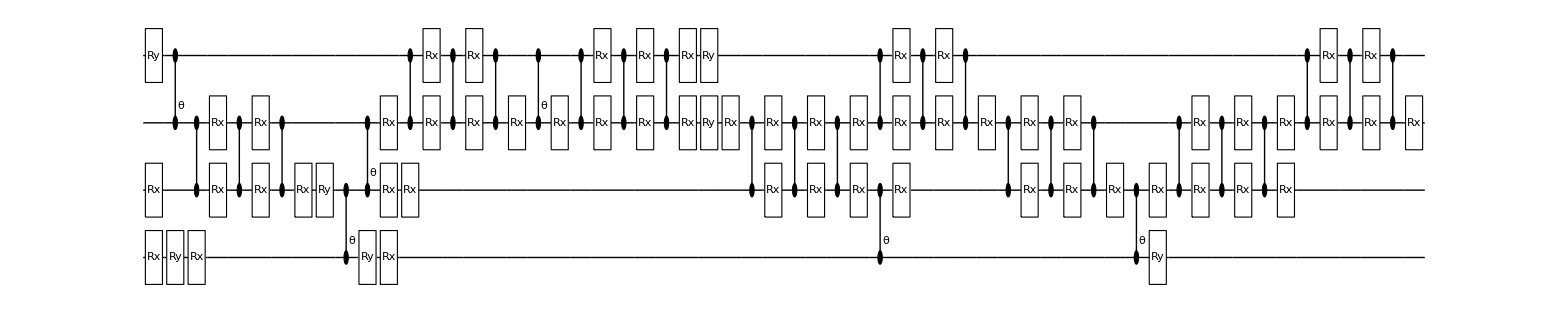

```mathematica
DrawCircuit[ansatz/.CustomGatesDefinitions,4]
```

```mathematica
HSDistance[ansatz/.CustomGatesDefinitions,θvars,unitary,4]
```

1.16544×10^-10

### Four qubits Silicon device

```mathematica
Options[SiliconDelft]={
qubitsNum->4,
T1->10^4,
T2-><|0-> 40.1,1-> 37.2,2-> 44.7,3-> 26.7|>,
QubitFreq-><|0-> 16.3*10^3,1-> 16.1*10^3,2-> 15.9*10^3,3-> 15.69*10^3|>,
RabiFreq-><|0->5,1->5,2->5,3->5|>,
OffResonantRabi->True,
StdPassiveNoise->True,
FidSingleXY-><|0-> 0.9996,1-> 0.9988,2-> 0.9991,3-> 0.9989|>,
EFSingleXY->{0,1},
FreqCZ-><|0-> 6.6,1-> 9.8,2-> 5.4|>,
FidCZ-><|0->0.9166807085341168,1->0.9805456134451412,2->0.9649648861853775|>,
EFCZ->{0,1},
ExchangeRotOn->{{0,0.07,0.042},{0.031,0,0.25},{0.02,0.03,0}},
ExchangeRotOff-><|0->0.03 ,1->0.02,2-> 0.028|>,
FidRead->0.99,
DurRead->10};
```

### Using various gradients

```mathematica
unitary=CalcCircuitMatrix[DeleteCases[GetKnownCircuit["QFT",4],Subscript[SWAP, __]]];
dev=SiliconDelft[];
confdef=checkedConfρ[dev,unitary,10,{0,1,2,3}];
```

```mathematica
grads={"NGAN","NGP","NGSTO","GPS","GPSTO","GCD","GCDSTO","GFD","GFDSTO"}
```

{NGAN,NGP,NGSTO,GPS,GPSTO,GCD,GCDSTO,GFD,GFDSTO}

```mathematica
qft4s=<||>;
```

```mathematica
Table[
conf=confdef;
  conf["grad"]=g;
res=CircuitSynthesis[4,conf];
qft4s[g]=res;
DumpSave["qft4s.mx",qft4s]
,{g,grads}];
```

Compilation with automatically generated ansatz at Wed 26 Oct 2022 00:05:15 with grad NGAN

@cycle1:Wed 26 Oct 2022 00:39:40, fev:562, <E>: 0.45890811965412953 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 7, 33}

I'm slowing down @cycle 2

@cycle2:Wed 26 Oct 2022 01:04:09, fev:842, <E>: 0.45890811965412953 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 7, 50}

I'm slowing down @cycle 3

@cycle3:Wed 26 Oct 2022 01:56:30, fev:1180, <E>: 0.45890811965412953 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 7, 88}

I'm slowing down @cycle 4

@cycle4:Wed 26 Oct 2022 04:59:00, fev:1639, <E>: 0.45890811965412953 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 7, 160}

Compilation with automatically generated ansatz at Wed 26 Oct 2022 05:03:37 with grad NGP

@cycle1:Wed 26 Oct 2022 05:06:56, fev:315, <E>: 1.0230067639871354 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 0, 0, 8, 34}

@cycle2:Wed 26 Oct 2022 05:12:50, fev:705, <E>: 0.8241295691833426 nansatz: 13 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 12, 68}

I'm slowing down @cycle 3

@cycle3:Wed 26 Oct 2022 05:16:37, fev:917, <E>: 0.8241295691833426 nansatz: 13 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 12, 95}

I'm slowing down @cycle 4

@cycle4:Wed 26 Oct 2022 05:24:26, fev:1193, <E>: 0.8241295691833426 nansatz: 13 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 12, 151}

I'm slowing down @cycle 5

@cycle5:Wed 26 Oct 2022 05:44:32, fev:1529, <E>: 0.8241295691833426 nansatz: 13 merged-smallθ-metric-bf-gmerged: {3, 6, 0, 12, 266}

Compilation with automatically generated ansatz at Wed 26 Oct 2022 05:45:13 with grad NGSTO

@cycle1:Wed 26 Oct 2022 06:12:39, fev:346, <E>: 0.7302434212138377 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 28}

I'm slowing down @cycle 2

@cycle2:Wed 26 Oct 2022 06:49:55, fev:560, <E>: 0.7302434212138377 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 51}

I'm slowing down @cycle 3

@cycle3:Wed 26 Oct 2022 08:31:42, fev:837, <E>: 0.7302434212138377 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 117}

I'm slowing down @cycle 4

@cycle4:Wed 26 Oct 2022 13:40:39, fev:1177, <E>: 0.7302434212138377 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 213}

Compilation with automatically generated ansatz at Wed 26 Oct 2022 13:48:19 with grad GPS

@cycle1:Wed 26 Oct 2022 14:10:42, fev:341, <E>: 0.6604320761228546 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 31}

I'm slowing down @cycle 2

@cycle2:Wed 26 Oct 2022 14:33:01, fev:564, <E>: 0.6604320761228546 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 45}

I'm slowing down @cycle 3

@cycle3:Wed 26 Oct 2022 15:36:23, fev:868, <E>: 0.6604320761228546 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 96}

I'm slowing down @cycle 4

@cycle4:Wed 26 Oct 2022 19:02:04, fev:1236, <E>: 0.6604320761228546 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 202}

Compilation with automatically generated ansatz at Wed 26 Oct 2022 19:03:11 with grad GPSTO

@cycle1:Wed 26 Oct 2022 19:25:39, fev:313, <E>: 0.8933182659912312 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 0, 0, 3, 41}

@cycle2:Wed 26 Oct 2022 20:02:26, fev:729, <E>: 0.7069339523495636 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 0, 0, 5, 65}

@cycle3:Wed 26 Oct 2022 21:15:44, fev:1190, <E>: 0.714468422050113 nansatz: 22 merged-smallθ-metric-bf-gmerged: {4, 0, 0, 9, 85}

I'm slowing down @cycle 4

@cycle4:Wed 26 Oct 2022 22:15:38, fev:1408, <E>: 0.714468422050113 nansatz: 22 merged-smallθ-metric-bf-gmerged: {4, 0, 0, 9, 119}

@cycle5:Thu 27 Oct 2022 02:40:13, fev:2056, <E>: 0.8782201086635528 nansatz: 41 merged-smallθ-metric-bf-gmerged: {5, 1, 0, 9, 175}

@cycle6:Thu 27 Oct 2022 15:30:23, fev:2919, <E>: 0.9973640249481285 nansatz: 51 merged-smallθ-metric-bf-gmerged: {11, 1, 0, 22, 239}

@cycle7:Fri 28 Oct 2022 09:46:49, fev:3809, <E>: 0.8869647148510357 nansatz: 57 merged-smallθ-metric-bf-gmerged: {18, 2, 0, 39, 325}

@cycle8:Sat 29 Oct 2022 08:28:22, fev:4839, <E>: 0.9533818632261228 nansatz: 79 merged-smallθ-metric-bf-gmerged: {19, 3, 0, 39, 417}

@cycle9:Mon 31 Oct 2022 05:21:10, fev:6710, <E>: 0.8834454740725238 nansatz: 76 merged-smallθ-metric-bf-gmerged: {25, 7, 0, 57, 540}

@cycle10:Tue 1 Nov 2022 09:47:03, fev:7851, <E>: 0.8968850122674809 nansatz: 84 merged-smallθ-metric-bf-gmerged: {28, 8, 0, 66, 609}

@cycle11:Wed 2 Nov 2022 20:43:27, fev:9079, <E>: 0.9749864042946073 nansatz: 90 merged-smallθ-metric-bf-gmerged: {31, 12, 0, 75, 728}

$Aborted